```mathematica
data=Get["/tmp/data.txt"];
data=Take[data,Length[data]-1];
```

```mathematica
F[entry_,id_]:=Module[
{i,r={id,0,0,0}},
For[i=1,i≤Length[entry⟦2⟧],i++,
If[entry⟦2,i,1⟧==id,
r=entry⟦2,i⟧
]
];
r
];
DrawCell[id_]:=Module[
{cell},
cell=Map[F[#,id]&,data];
Show[
{ListPlot[Map[#⟦2⟧&,cell],Joined->True,PlotStyle->Blue],
ListPlot[Map[#⟦3⟧&,cell],Joined->True,PlotStyle->Orange],
ListPlot[Map[180/(2π)#⟦4⟧&,cell],Joined->True,PlotStyle->Green]},PlotRange->All
]
]
```

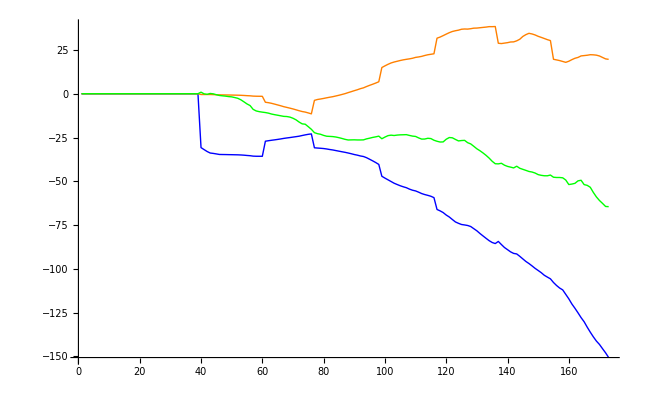

```mathematica
Show[DrawCell[2]]
```